```mathematica
n=1000; m=1000;
```

```mathematica
(*En este codigo, se leen los datos exportados, se hace el grafo t, y la contraparte aleatoria r. Se analizan las componentes conexas y se añaden las componentes correspondientes a puntos singulares o asilados del grafo. En los vectores de 1001 elementos, scct y sccr, se almacena la cantidad de veces que se registró un tamaño i para la componente gigante, como un número entero en la posición i+1 del vector. Al exportar, buscamos una densidad de probabilidad en un histograma con ancho del bin=1, por lo que simpemente cada elemento _{i} de dicho vector sera dividido por Total[vect]*)
```

```mathematica
kaux={};  distt=ConstantArray[0,1000]; distr=ConstantArray[0, 1000]; diamt={}; diamr={};Do[kaux={};cc={}; x=0;  {spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0167.txt"]]]; While[spression≠ {0,0}, {kaux=Join[kaux, {spression}],  spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0167.txt"]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n], (*Print["se genero la red t y r"]*),f=DeleteCases[Flatten[UpperTriangularize[GraphDistanceMatrix[Subgraph[t, First[ConnectedComponents[t]]]]]], 0],(*Print["se sacaron las distancias"]*), Do[{distt[[i]]=distt[[i]]+2*Count[f, i]}, {i, 1, 100}],(*Print["se guardaron las distancias en el vector"]*), diamt=Join[diamt, {Max[f]}], f=DeleteCases[Flatten[UpperTriangularize[GraphDistanceMatrix[Subgraph[r, First[ConnectedComponents[r]]]]]], 0], Do[{distr[[i]]=distr[[i]]+2*Count[f, i]}, {i, 1, 100}], diamr=Join[diamr, {Max[f]}]} , m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*Analisis de d en kinship*)
```

```mathematica
T=Total[distt]; M=N[Sum[{i*distt[[i]]}, {i, 1, Length[distt]}]/T];Print[M];SD=N[Sqrt[Sum[distt[[i]]*(i-M)^2, {i, 1, Length[distt]}]/(T-1)]]; Print[SD];
```

{3.10173}

{0.68951}

```mathematica
(*Analisis de d en random*)
```

```mathematica
T=Total[distr]; M=N[Sum[{i*distr[[i]]}, {i, 1, Length[distt]}]/T];Print[M];SD=N[Sqrt[Sum[distr[[i]]*(i-M)^2, {i, 1, Length[distt]}]/(T-1)]]; Print[SD];
```

{2.85938}

{0.572377}

```mathematica
(*Analisis de D en Kinship y random*)
```

```mathematica
Print[N[Mean[diamt]]];Print[N[StandardDeviation[diamt]]];Print[N[Mean[diamr]]];Print[N[StandardDeviation[diamr]]];
```

5.001

0.0316228

4.732

0.46518

```mathematica
(*RANDOM NETWORKS*)
```

```mathematica
n=1000; α=1.; m=10; distr=ConstantArray[0, 1000]; diamr={}; r=RandomGraph[{n,Round[3*α*n/2]}]; f=DeleteCases[Flatten[UpperTriangularize[GraphDistanceMatrix[Subgraph[r, First[ConnectedComponents[r]]]]]], 0]; Do[{distr[[i]]=distr[[i]]+2*Count[f, i]}, {i, 1, 100}];  diamr=Join[diamr, {Max[f]}];
```

```mathematica
n=1000; α=0.29; m=10; distr=ConstantArray[0, 1000]; diamr={}; Do[{ r=RandomGraph[{n,Round[3*α*n/2]}], f=DeleteCases[Flatten[UpperTriangularize[GraphDistanceMatrix[Subgraph[r, First[ConnectedComponents[r]]]]]], 0], Do[{distr[[i]]=distr[[i]]+2*Count[f, i]}, {i, 1, 100}],diamr=Join[diamr, {Max[f]}] },m]
```

```mathematica
(*Export distances*)
```

```mathematica
T=Total[distr]; M=N[Sum[{i*distr[[i]]}, {i, 1, Length[distr]}]/T];Print[M];SD=N[Sqrt[Sum[distr[[i]]*(i-M)^2, {i, 1, Length[distr]}]/(T-1)]]; Print[SD];
```

{2.19429}

{1.03629}

```mathematica
(*Export diameter*)
```

```mathematica
Print[N[Mean[diamr]]];Print[N[StandardDeviation[diamr]]];
```

13.7

0.823273

```mathematica
(*RANDOM NETWORKS FULL AUTOMATHIZED*)
```

```mathematica
n=1000; m=2; distr=Table[ConstantArray[0, 1000], 20]; diamr=Table[{}, 20]; For[j=1,j≤20, j++, {α=0.1*j, Do[{ r=RandomGraph[{n,Round[3*α*n/2]}], f=DeleteCases[Flatten[UpperTriangularize[GraphDistanceMatrix[Subgraph[r, First[ConnectedComponents[r]]]]]], 0], Do[{distr[[j,i]]=distr[[j,i]]+2*Count[f, i]}, {i, 1, 100}],diamr[[j]]=Join[diamr[[j]], {Max[f]}] },m]}]
```

```mathematica
(*EXPORT MEAN DISTANCE*)
```

```mathematica
meandistance=Table[ N[Sum[j*distr[[i,j]], {j, 1, Length[distr[[i]]]}]/Total[distr[[i]]]], {i,1,20}];
```

```mathematica
(*EXPORT STANDART DEVIATION OF DISTANCE*)
```

```mathematica
standarddevdist=Table[N[Sqrt[Sum[distr[[i,j]]*(j-meandistance[[i]])^2, {j, 1, Length[distr[[i]]]}]/(Total[distr[[i]]]-1)]], {i,1,20}];
```

```mathematica
(*PLOT OF DISTANCE*)
```

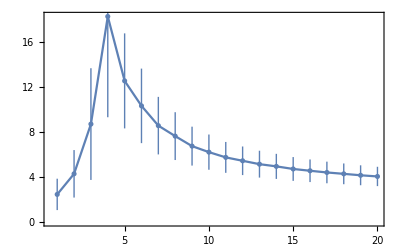

```mathematica
ListPlot[Table[Around[meandistance[[i]], standarddevdist[[i]] ], {i,1,Length[meandistance]}], Frame->True, PlotRange->All, Joined->True, Mesh->All]
```

```mathematica
(*EXPORT MEAN DIAMETER*)
```

```mathematica
meandiametro=Table[N[Mean[diamr[[i]]]], {i,1,Length[diamr]}];
```

```mathematica
(*EXPORT STANDART DEVIATION OF DIAMETER*)
```

```mathematica
standartdiametro=Table[N[StandardDeviation[diamr[[i]]]], {i,1,Length[diamr]}];
```

```mathematica
(*PLOT DIAMETER*)
```

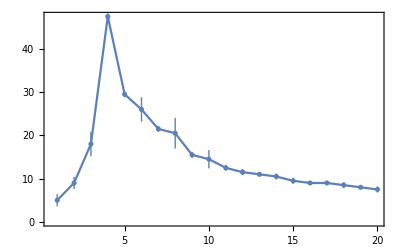

```mathematica
ListPlot[Table[Around[meandiametro[[i]], standartdiametro[[i]] ], {i,1,Length[meandiametro]}], Frame->True, PlotRange->All, Joined->True, Mesh->All]
```